```mathematica
(* a first order ODE where u2[t] is given *)
γ = 1/2;
U2[t_] := 0.25 Sin[2π t];
x = {-1, 0, 1};
u0 = {0,U2[0],0};
f[t_] := 10{-t, 0, t^2};
tmax = 1.0;
n = 80;
dt = tmax / n;
MM = ({{2, 1, 0}, {1, 4, 1}, {0, 1, 2}});
KK = 100({{1, -1, 0}, {-1, 2, -1}, {0, -1, 1}});
F = ({{1, 0, 0}, {0, 0, 0}, {0, 0, 1}});

soln = NDSolve[{
(MM.{u1'[t], U2'[t], u3'[t]} + KK.{u1[t], U2[t], u3[t]})[[{1,3}]] == f[t][[{1,3}]] ,
u1[0] == u0[[1]],u3[0] == u0[[3]]
}, {u1[t], u3[t]}, {t, 0, tmax}][[1]];
derivatives = {u1'[t]->D[u1[t] /. soln, t], u3'[t]->D[u3[t] /. soln, t]};
```

```mathematica
error[n_] := Module[{dt = tmax/n},
TT=MM+γ KK dt;
TT[[2]] = IdentityMatrix[3][[2]];
TT[[All, 2]] = IdentityMatrix[3][[All, 2]];

u=u0;
H=MM;
H[[2]] = IdentityMatrix[3][[2]];
H[[All, 2]] = IdentityMatrix[3][[All, 2]];
dudt = LinearSolve[H, f[0] - KK.u - MM.{0, U2'[0], 0}];
dudt[[2]] = U2'[0];
τ=0;
xHistory={x+u};
vHistory={dudt};
Do[
τ+=dt;
fc=MM.{0, U2'[τ], 0} + KK.{0, U2[τ], 0};
rhs=f[τ]-fc -KK.F.(u+ (1-γ)dudt*dt);
rhs[[2]]=0;
dudtprev = dudt;
dudt=LinearSolve[TT,rhs];
dudt[[2]]=U2'[τ];
u+=((1-γ)dudtprev + γ dudt)dt;
u[[2]]=U2[τ];
AppendTo[xHistory, x +u];
AppendTo[vHistory, dudt];
,
{i, 1, n}
];
u - (({u1[t], U2[t], u3[t]}) /. soln) /. t->τ
]

(* for a second order method, we expect the error to reduce by a factor of 4 when halving the timestep (asymptotically) *)
errors = Table[error[2^i * 10], {i, 0, 6}]; errors // MatrixForm
errors[[1;;-2, {1, 3}]]/errors[[2;;-1, {1, 3}]]
```

(-0.000998481 | 0. | -0.00099808
-0.000244808 | 0. | -0.000244808
-0.0000607676 | 0. | -0.0000607676
-0.0000151637 | 0. | -0.0000151637
-3.78787×10^-6 | 0. | -3.78787×10^-6
-9.45488×10^-7 | 0. | -9.45488×10^-7
-2.34989×10^-7 | 0. | -2.34989×10^-7)

{{4.07863,4.07699},{4.0286,4.0286},{4.00744,4.00744},{4.00322,4.00322},{4.00626,4.00626},{4.02354,4.02354}}

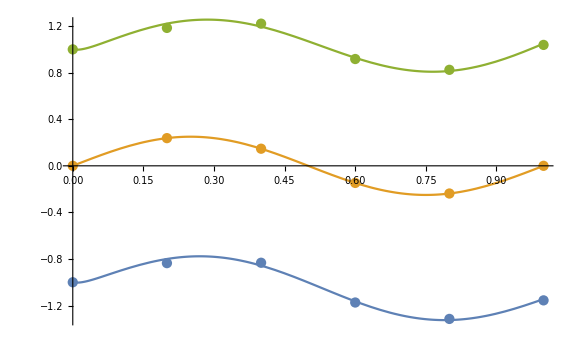

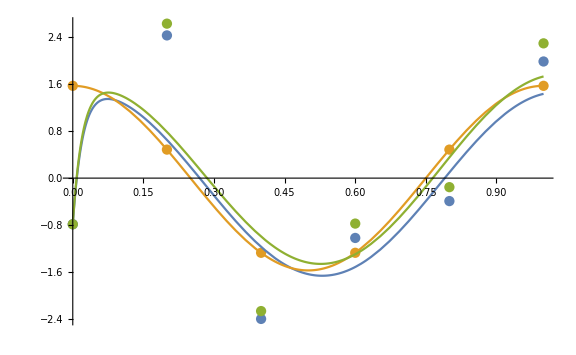

```mathematica
error[5];
Show[
ListPlot[Transpose[xHistory], DataRange->{0,tmax}],
Plot[Evaluate[(x+{u1[t], U2[t], u3[t]}) /. soln], {t, 0,tmax}],
ImageSize->Large
]

Show[
ListPlot[Transpose[vHistory], DataRange->{0, tmax}],
Plot[Evaluate[({u1'[t], U2'[t], u3'[t]}) /. derivatives], {t, 0, tmax}],
ImageSize->Large
]
```

```mathematica
H
```

{{2,0,0},{0,1,0},{0,0,2}}

```mathematica
(* a second order ODE where u2[t] is given *)
γ = 1/2;
β = 1/6;
U2[t_] := 0.25 Cos[2π t]^4;
x = {-1, 0, 1};
u0 = {0,U2[0],0};
dudt0 = {1, U2'[0], 0};
f[t_] := 10{-t, 0, t^2};
tmax = 1.0;
n = 80;
dt = tmax / n;
MM = ({{2, 1, 0}, {1, 4, 1}, {0, 1, 2}});
CC = ({{1, -1, 0}, {-1, 2, -1}, {0, -1, 1}});
KK = 100({{1, -1, 0}, {-1, 2, -1}, {0, -1, 1}});


F = ({{1, 0, 0}, {0, 0, 0}, {0, 0, 1}});


soln = NDSolve[{
(MM.{u1''[t], U2''[t], u3''[t]} + CC.{u1'[t], U2'[t], u3'[t]} + KK.{u1[t], U2[t], u3[t]})[[{1,3}]] == f[t][[{1,3}]] ,
u1[0] == u0[[1]], u1'[0] == dudt0[[1]],
u3[0] == u0[[3]], u3'[0] == dudt0[[3]]
}, {u1[t], u3[t]}, {t, 0, tmax}][[1]];
derivatives = {u1'[t]->D[u1[t] /. soln, t], u3'[t]->D[u3[t] /. soln, t]};
```

```mathematica
error[n_] := Module[{dt = tmax/n},
TT=MM+γ CC dt+β KK dt^2;
TT[[2]] = IdentityMatrix[3][[2]];
TT[[All, 2]] = IdentityMatrix[3][[All, 2]];
H=MM;
H[[2]] = IdentityMatrix[3][[2]];
H[[All, 2]] = IdentityMatrix[3][[All, 2]];
u=u0;
dudt=dudt0;
d2udt2 = LinearSolve[H, f[0] - CC.dudt - KK.u - MM.{0, U2''[0], 0}];
d2udt2[[2]] = U2''[0];
τ=0;
xHistory={x+u};
vHistory={dudt};
Do[
τ+=dt;
fc = MM.{0, U2''[τ], 0}+ CC.{0, U2'[τ], 0} + KK.{0, U2[τ], 0};
rhs=f[τ]-fc - CC.F.(dudt+(1-γ)d2udt2 * dt)-KK.F.(u+ dudt*dt+(1/2-β)d2udt2 * dt^2);
rhs[[2]]=0;
d2udt2prev = d2udt2;
d2udt2=LinearSolve[TT,rhs];
u+=dudt*dt+((1-2β)d2udt2prev + 2β d2udt2)dt^2/2;
dudt+=((1-γ)d2udt2prev + γ d2udt2)dt;
d2udt2[[2]] = U2''[τ];
dudt[[2]] = U2'[τ];
u[[2]] = U2[τ];
AppendTo[xHistory, x +u];
AppendTo[vHistory, dudt];
,
{i, 1, n}
];
u - (({u1[t], U2[t], u3[t]}) /. soln) /. t->τ
]

(* for a second order method, we expect the error to reduce by a factor of 4 when halving the timestep (asymptotically) *)
errors = Table[error[2^i * 10], {i, 0, 6}];
errors[[1;;-2, {1, 3}]]/errors[[2;;-1, {1, 3}]]
```

{{2.74615,3.20921},{3.68106,3.79344},{3.91966,3.94765},{3.97988,3.98694},{3.995,3.99705},{3.99887,4.00054}}

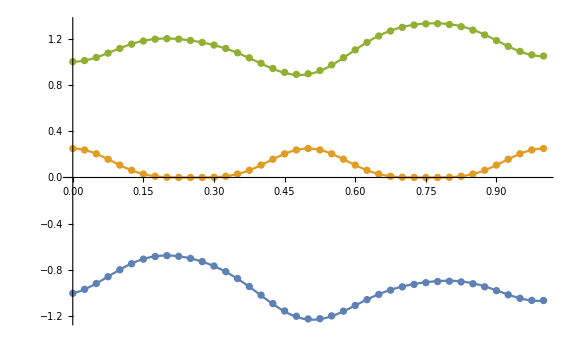

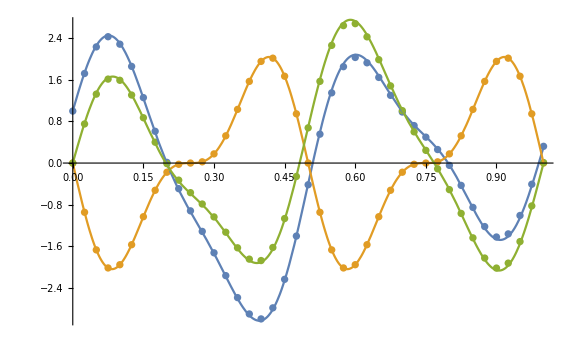

```mathematica
error[40];
Show[
ListPlot[Transpose[xHistory], DataRange->{0,tmax}],
Plot[Evaluate[(x+{u1[t], U2[t], u3[t]}) /. soln], {t, 0,tmax}],
ImageSize->Large
]

Show[
ListPlot[Transpose[vHistory], DataRange->{0, tmax}],
Plot[Evaluate[({u1'[t], U2'[t], u3'[t]}) /. derivatives], {t, 0, tmax}],
ImageSize->Large
]
```